```mathematica
TempoToRadians[tempo_]:=π/2-2π*Log[2,tempo/90]
SetAttributes[TempoToRadians,Listable];
```

```mathematica
FlipQ[tempo_]:=Mod[TempoToRadians[tempo],2π]>π
```

```mathematica
marks={
Circle[{0,0},1],
{Thickness[0.002],Table[
Rotate[Line[{{0,0.3+0*(i-90)/360},{0,1.1}}],-2π*(Log[2,(i)/90]),{0,0}]
,{i,90,179,10}]},
{Thickness[0.002],Opacity[0.1
],Table[
Rotate[Line[{{0,0.3+0*(i-90)/360},{0,1.1}}],-2π*(Log[2,(i)/90]),{0,0}]
,{i,95,179,10}]},
{Thickness[0.001],Table[
{If[EvenQ[i],Opacity[1],Opacity[(210-i)/90]],Rotate[Line[{{0,0.95},{0,1.05}}],-2π*(Log[2,(i)/90]),{0,0}]}
,{i,90,179}]},
{Thickness[0.001],Table[
{Opacity[(200-i)/90],Rotate[Line[{{0,0.95},{0,1.05}}],-2π*(Log[2,(i)/90]),{0,0}]}
,{i,181,200,2}]}
};
```

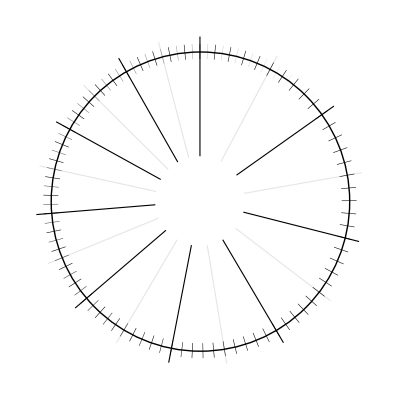

```mathematica
Graphics[marks]
```

```mathematica
MakeTempoLabel[{str_,val_,dist_}]:=Translate[Style[Text[str],FontSize->Scaled[0.025]],{dist*Cos[TempoToRadians[val]],dist*Sin[TempoToRadians[val]]}]
```

```mathematica
MakeTempoLabel[{str_,tempo_,flipQ_}]:=Rotate[Translate[Rotate[Style[Text[str],FontSize->Scaled[0.025],
FontFamily->"Helvetica"],If[flipQ,π,0]],{0,1.15}],-2π*Log[2,tempo/90],{0,0}]
```

```mathematica
Graphics[{
marks,
MakeTempoLabel/@tempoLabels
}]//Dynamic
```

```mathematica
temposUnRounded={{1, "Cross-Step Waltz", 108, 114, 120, 124}, {1, "Fast Waltz", 160, 170, 200, 210}, {1, "Rotary Waltz", 135, 140, 160, 170}, {2, "Lindy Hop", 135, 140, 170, 180}, {2, "Sweet Lindy", 110, 115, 135, 140}, {3, "6-Count Swing", 80, 85, 105, 115}, {3, "East Coast Swing", 115, 120, 140, 145}, {4, "West Coast Swing", 90, 100, 120, 130}, {5, "Cha-Cha", 112, 118, 122, 126}, {5, "Salsa", 85, 90, 100, 110}, {6, "Foxtrot", 130, 135, 170, 180}, {6, "One-Step", 110, 115, 130, 135}, {6, "Quickstep", 85, 90, 105, 110}, {7, "Polka", 105, 110, 120, 125}, {7, "Schottische", 150, 155, 165, 170}, {8, "Tango", 115, 120, 130, 140}, {9, "Hustle", 110, 115, 125, 130}, {9, "Club 2-Step", 75, 80, 85, 90}, {10, "Merengue", 110, 115, 130, 135}};
```

```mathematica
MakeSlider[{_,danceName_,__}]:=Framed[Grid[{{danceName,ColorSlider[Dynamic[tempoColor[danceName]]]}}]]
```

```mathematica
(* Serialize colors *)
tempoColor/@tempos[[All,2]]
```

```mathematica
(tempoColor[#[[1]]]=#[[2]])&/@({tempos[[All,2]],{RGBColor[1.,0.7310444800488288,0.06666666666666667],RGBColor[0.7333333333333333,0.,0.],RGBColor[1.,0.5705806057831693,0.3333333333333333],RGBColor[0.4,0.4508735790035859,1.],RGBColor[0.2,0.7966430151827267,1.],RGBColor[0.,0.9333333333333333,0.6485694666971847],RGBColor[0.06666666666666667,1.,0.47794308384832535],RGBColor[0.,0.36047913328755626,0.7333333333333333],RGBColor[1.,0.44632639047837036,0.06666666666666667],RGBColor[0.8666666666666667,0.22026398107881284,0.],RGBColor[0.,0.8,0.10847638666361487],RGBColor[0.,0.5333333333333333,0.07231250476844435],RGBColor[0.7175555046921492,1.,0.3333333333333333],RGBColor[0.15825131609063858,0.9333333333333333,0.],RGBColor[1.,0.,0.45767910276951246],RGBColor[0.9333333333333333,0.8067444876783398,0.],RGBColor[0.6044861524376287,0.06666666666666667,1.],RGBColor[0.06666666666666667,0.6678110933089189,1.],RGBColor[1.,0.4666666666666667,0.8463569085221637]}}//Transpose)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Blend[tempoColor[danceName]
```

```mathematica
Font
```

```mathematica
DanceToGraphics[{ringIndex_,danceName_,longStart_,midStart_,midEnd_,longEnd_,flipQ_,textOffset_}]:={
EdgeForm[CapForm["None"]],
tempoColor[danceName],
{CapForm["Square"],Thickness[0.002],Circle[{0,0},1-(ringIndex+0.5)/15-0.00225,TempoToRadians[{longStart,midStart}]+inOffset*(1+ringIndex/8)]},
{Thickness[0.008],Circle[{0,0},1-(ringIndex+0.5)/15,TempoToRadians[{midStart,midEnd}]+thickOffset*(1+ringIndex/8)]},
{Thickness[0.002],Circle[{0,0},1-(ringIndex+0.5)/15+0.00225,TempoToRadians[{midEnd,longEnd}]+outOffset*(1+ringIndex/8)]},
{Blend[{tempoColor[danceName],Black},0.5],Rotate[
Translate[
Rotate[
Translate[
Style[
Text[" "<>danceName<>" "],
Background->Opacity[0.85,Blend[{tempoColor[danceName],White},0.8]],
FontSize->Scaled[0.02],
FontFamily->"Helvetica"]
,{0,textOffset}
],
If[flipQ,π,0],{0,0}]
,{0,1-(ringIndex+0.5)/15}
],
-2π*Log[2,((midStart+midEnd)/2)/90],{0,0}]}
}
```

```mathematica
TempoToRadians[120]//N
```

-1.03696

```mathematica
MakeSlider/@tempos
```

{Cross-Step Waltz | Cross-Step Waltz,Fast Waltz | Fast Waltz,Rotary Waltz | Rotary Waltz,Lindy Hop | Lindy Hop,Sweet Lindy | Sweet Lindy,6-Count Swing | 6-Count Swing,East Coast Swing | East Coast Swing,West Coast Swing | West Coast Swing,Cha-Cha | Cha-Cha,Salsa | Salsa,Foxtrot | Foxtrot,One-Step | One-Step,Quickstep | Quickstep,Polka | Polka,Schottische | Schottische,Tango | Tango,Hustle | Hustle,Club 2-Step | Club 2-Step,Merengue | Merengue}

```mathematica
tempos={{1, "Cross-Step Waltz", 105, 114, 122, 125, True, 0.01}, {1, "Fast Waltz", 160, 170, 200, 210, False, 0.0}, {1, "Rotary Waltz", 135, 140, 160, 170, False, 0.005}, {2, "Lindy Hop", 135, 140, 170, 180, False, -0.005}, {2, "Sweet Lindy", 110, 115, 135, 140, True, 0.0}, {3, "6-Count Swing", 80, 85, 105, 115, False, 0.01}, {3, "East Coast Swing", 115, 120, 140, 145, True, 0.03}, {4, "West Coast Swing", 90, 100, 120, 130, True, 0.01}, {5, "Cha-Cha", 110, 115, 125, 130, True, 0.00}, {5, "Salsa", 85, 90, 100, 110, False, 0.01}, {6, "Foxtrot", 130, 135, 170, 180, False, 0.0}, {6, "One-Step", 110, 115, 130, 135, True, 0.02}, {6, "Quickstep", 85, 90, 105, 110, False, 0.0}, {7, "Polka", 105, 110, 120, 125, True, 0.01}, {7, "Schottische", 150, 155, 165, 170, False, -0.06}, {8, "Tango", 115, 120, 130, 140, True, 0.01}, {9, "Hustle", 110, 115, 125, 130, True, 0.01}, {9, "Club 2-Step", 75, 80, 85, 90, False, -0.06}, {10, "Merengue", 110, 115, 130, 135, True, 0.015}};
```

```mathematica
title={
Translate[Style[Text["A Unified Chart of Social Dance Tempos"],
FontSize->Scaled[0.04],FontFamily->"Helvetica"],{0,1.45}],
Translate[Style[Text["Lucas Garron – v1.0 – October 2015"],
FontSize->Scaled[0.03],FontFamily->"Helvetica"],{0,1.35}],
};
```

```mathematica
tempoLabels = {{"90 ⁄ 180", 90, False}, {"100", 100, False}, {"110", 110, True}, {"120", 120, True}, {"130", 130, True}, {"140", 140, True}, {"75 ⁄ 150", 150, False}, {"80 ⁄ 160", 160, False}, {"85 ⁄ 170", 170, False}}
```

{{90 ⁄ 180,90,False},{100,100,False},{110,110,True},{120,120,True},{130,130,True},{140,140,True},{75 ⁄ 150,150,False},{80 ⁄ 160,160,False},{85 ⁄ 170,170,False}}

```mathematica
graphic:=Graphics[{
{Opacity[1],White,Rectangle[{-1.4,-1.3},{1.4,1.7}]},
title,
marks,
MakeTempoLabel/@tempoLabels,
DanceToGraphics/@tempos
},
ImagePadding->20]
```

```mathematica
Dynamic[graphic]
```

```mathematica
thickOffset ={0,0};
inOffset ={-0,0};
outOffset ={0,0};
Export["social-dance-tempos.svg",graphic,ImageSize->2048,ImagePadding->100]
```

social-dance-tempos.svg

```mathematica
thickOffset ={-0.01,0.01};
inOffset ={-0.002,0.00};
outOffset ={0,0.004};
Export["social-dance-tempos.png",graphic,ImageSize->4096,ImagePadding->100,Background->None]
```

social-dance-tempos.png

### Additional:

#### Fast Waltz : arrow Salsa to Cha-Cha: dotted 4-Count to 6-Count: dotted Cross-Step to Rotary: dotted Rotary to Fast Waltz: dotted